```mathematica
x={3.2,1.41,1.01,1.11};
```

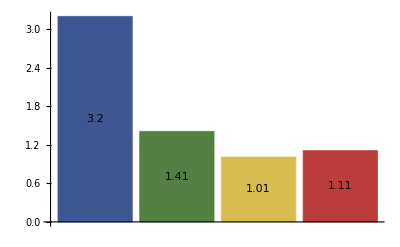
-Graphics--Graphics- | Korištenje djeljene memorije
-Graphics- | Izbjegavanje bank konflikata
-Graphics- | Stapanje memorije
-Graphics- | Odmotavanje petlji

```mathematica
BarChart[x,ChartLegends->{"Korištenje djeljene memorije","Izbjegavanje bank konflikata","Stapanje memorije","Odmotavanje petlji"},ChartStyle->"DarkRainbow",ChartLabels->Placed[x,{1/2,1/2}]]
```

```mathematica
t={4590,4162,4127,4202,4310};
```

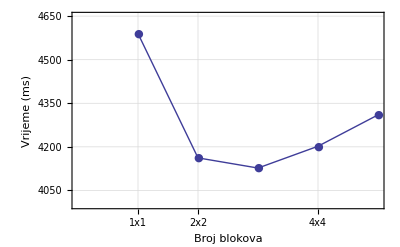

```mathematica
l1=ListPlot[t, PlotRange->{4000,4650},FrameTicks->{{{1,"1x1"},{1,"1x1"},{2,"2x2"},{3,"3x3"},{4,"4x4"},{5,"5x5"}},Automatic},FrameLabel->{"Broj blokova","Vrijeme (ms)"},Frame->{{True, False}, {True, False}},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small}]
```

```mathematica
Export["blokovi.pdf",l1]
```

blokovi.pdf

```mathematica
gemm={5.44,2.52,2.49,  1.15,1 };
```

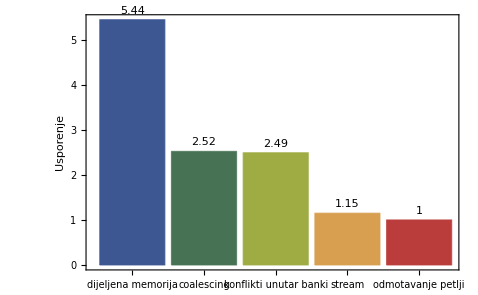

```mathematica
l2=BarChart[gemm,ChartStyle->"DarkRainbow",ChartLabels->Placed[gemm,Above],Frame->{{True, False}, {True, False}},FrameTicks->{{{1,"dijeljena memorija"},{2,"coalescing"},{3,"konflikti unutar banki"},{4,"stream"},{5,"odmotavanje petlji"}},Automatic},FrameLabel->{"","Usporenje"}]
```

```mathematica
Export["usporenja.pdf",l2]
```

usporenja.pdf

```mathematica
i5Single=Import["C:\\Users\\Dejan\\Documents\\single_rez.txt","Table"];
```

```mathematica
gfSingle=Import["C:\\Users\\Dejan\\Documents\\single_gpu_rez.txt","Table"];
```

```mathematica
teslaSingle=Import["C:\\Users\\Dejan\\Documents\\tesla_single.txt","Table"];
```

```mathematica
xeonSingle=Import["C:\\Users\\Dejan\\Documents\\xeon_single.txt","Table"];
```

```mathematica
x=Range[35];
```

```mathematica
<<PlotLegends`;
```

```mathematica
sBrzina=ListPlot[{cpuSingle[[All,2]],xeonSingle[[All,2]],gpuSingle[[All,2]], teslaSingle[[All,2]]}, PlotRange->{0,41000},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],teslaSingle[[#,1]]}&,Range[1,31,3]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Vrijeme (ms)"},PlotLegend->{"Intel Core i5-760 (MATLAB - 4 dretve)","Intel Xeon E5620 (MATLAB - 8 dretvi)","Nvidia GeForce GTX 460","Nvidia Tesla M2050"},LegendShadow->None,LegendPosition->{-0.67,0.28},LegendSize->{1,0.3},LegendTextSpace->6]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol :: argx will be suppressed during this calculation.

Part::partd: Part specification teslaSingle ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification teslaSingle ⟦ 4, 1 ⟧ is longer than depth of object.

Part::partd: Part specification teslaSingle ⟦ 7, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

```mathematica
Dimensions[teslaSingle]
```

{31,3}

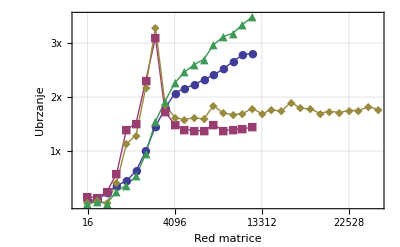

```mathematica
sUbrzanje=ListPlot[{cpuSingle[[All,2]]/gpuSingle[[All,2]],xeonSingle[[1;;18,2]]/gpuSingle[[All,2]],xeonSingle[[All,2]]/teslaSingle[[All,2]],cpuSingle[[All,2]]/teslaSingle[[1;;18,2]]}, PlotRange->{0,3.5},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small}, FrameTicks->{Map[{x[[#]],teslaSingle[[#,1]]}&,Range[1,31,3]],{{1,"1x"},{2,"2x"},{3,"3x"}}},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Ubrzanje"},PlotLegend->{"GeForce GTX 460 - Core i5-760 (4 dretve)", "GeForce GTX 460 - Xeon E5620 (8 dretvi)", "Tesla M2050 - Xeon E5620 (8 dretvi)","Tesla M2050 - Core i5-760 (4 dretve)"},LegendShadow->None,LegendPosition->{-0.4,-0.43},LegendSize->{1,0.3},LegendTextSpace->6]
```

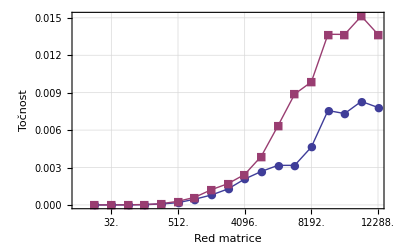

```mathematica
sTocnost=ListPlot[{cpuSingle[[All,4]],cpuSingle[[All,5]]},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],cpuSingle[[#,1]]}&,Range[2,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Core i5-760 (MATLAB)","GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.7,0.2},LegendSize->{0.9,0.25},LegendTextSpace->6]
```

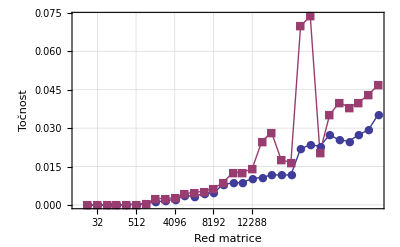

```mathematica
sTocnost=ListPlot[{xeonSingle[[All,4]],xeonSingle[[All,5]]},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],teslaSingle[[#,1]]}&,Range[2,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Core i5-760 (MATLAB)","GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.7,0.2},LegendSize->{0.9,0.25},LegendTextSpace->6]
```

```mathematica
cpuDouble=Import["C:\\Users\\Dejan\\Documents\\double_rez.txt","Table"];
```

```mathematica
gpuDouble=Import["C:\\Users\\Dejan\\Documents\\double_gpu_rez.txt","Table"];
```

```mathematica
teslaDouble=Import["C:\\Users\\Dejan\\Documents\\tesla_double.txt","Table"];
```

```mathematica
xeonDouble=Import["C:\\Users\\Dejan\\Documents\\xeon_double.txt","Table"];
```

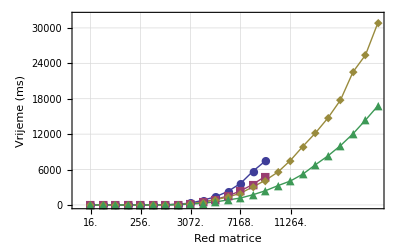

```mathematica
dBrzina=ListPlot[{cpuDouble[[All,2]],gpuDouble[[All,2]], xeonDouble[[All,2]],teslaDouble[[All,2]]}, PlotRange->{0,32000},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],cpuSingle[[#,1]]}&,Range[1,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Vrijeme (ms)"},PlotLegend->{"Intel Core i5-760 (MATLAB)","GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.7,0.2},LegendSize->{0.9,0.25},LegendTextSpace->6]
```

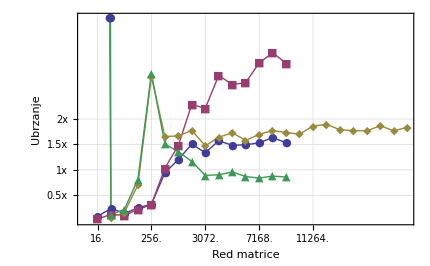

```mathematica
dUbrzanje=ListPlot[{cpuDouble[[All,2]]/gpuDouble[[All,2]],cpuDouble[[All,2]]/teslaDouble[[1;;15,2]],xeonDouble[[All,2]]/teslaDouble[[All,2]],xeonDouble[[1;;15,2]]/gpuDouble[[All,2]]}, PlotRange->{0,4},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small}, FrameTicks->{Map[{x[[#]],cpuSingle[[#,1]]}&,Range[1,18,2]],{{0.5,"0.5x"},{1,"1x"},{1.5,"1.5x"},{2,"2x"}}},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Ubrzanje"}]
```

```mathematica
Dimensions[cpuDouble]
```

{15,5}

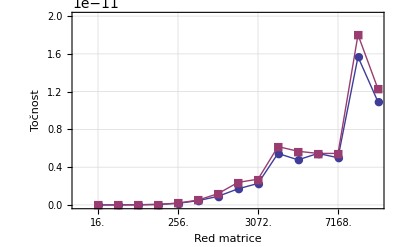

```mathematica
dTocnost1=ListPlot[{cpuDouble[[All,4]],cpuDouble[[All,5]]},PlotRange->{0, 2*10^-11},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],cpuSingle[[#,1]]}&,Range[1,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Core i5-760 (MATLAB)","GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.55,0.2},LegendSize->{0.9,0.25},LegendTextSpace->6]
```

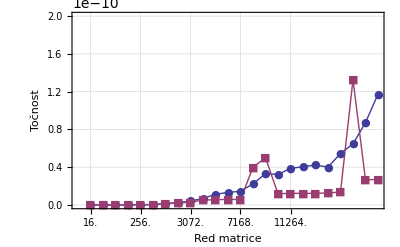

```mathematica
dTocnost2=ListPlot[{xeonDouble[[All,4]],xeonDouble[[All,5]]},PlotRange->{0, 2*10^-10},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],xeonSingle[[#,1]]}&,Range[1,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Core i5-760 (MATLAB)","GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.55,0.2},LegendSize->{0.9,0.25},LegendTextSpace->6]
```

```mathematica
Export["sBrzina.pdf",sBrzina]
```

sBrzina.pdf

```mathematica
Export["dBrzina.pdf",dBrzina]
```

dBrzina.pdf

```mathematica
Export["sUbrzanje.pdf",sUbrzanje]
```

sUbrzanje.pdf

```mathematica
Export["dUbrzanje.pdf",dUbrzanje]
```

dUbrzanje.pdf

```mathematica
Export["dTocnost.pdf",dTocnost]
```

dTocnost.pdf

```mathematica
Export["sTocnost.pdf",sTocnost]
```

sTocnost.pdf